# Projekt za Računalniška orodja v matematiki

## Analiza bruto plače v Sloveniji in po svetu 31. 8. 2023

## Pridobivanje podatkov

Podatke sem pridobil s strani stat.si in https://www.oecd.org/ .
Podatki so shranjeni v podmapi “podatki” in so v CSV obliki.

## Povprečna plača v Sloveniji 2014-2023

Spodaj imamo grafe ki nam prikazuje povprečno bruto plačo v Sloveniji med letom 2014 in 2023.

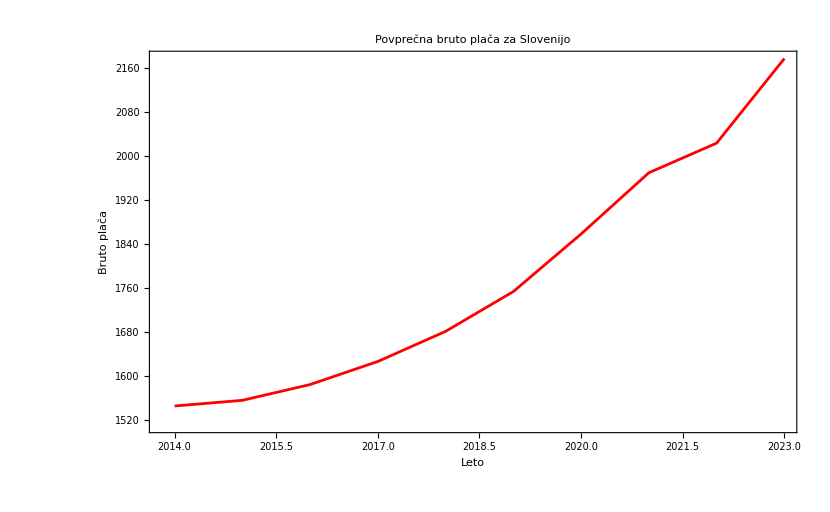

-Graphics-

```mathematica
dataSLO = Import["C:\\Users\\Marko\\Documents\\Wolfram Mathematica\\podatki\\slovenija.csv",HeaderLines->3];
mesec = dataSLO[[All,2]];
placa = dataSLO[[All,3]];

vsaLeta = List[2014,2015,2016,2017,2018,2019,2020,2021,2022,2023];

avgLeto2014 = Total[placa[[;;12]]]/ 12;
placa = Drop[placa, 12];
placaLeta = List[avgLeto2014];

avgLeto2015 = Total[placa[[;;12]]]/ 12;
AppendTo[placaLeta, avgLeto2015];
placa = Drop[placa, 12];
avgLeto2016 = Total[placa[[;;12]]]/ 12;
AppendTo[placaLeta, avgLeto2016];
placa = Drop[placa, 12];
avgLeto2017 = Total[placa[[;;12]]]/ 12;
AppendTo[placaLeta, avgLeto2017];
placa = Drop[placa, 12];
avgLeto2018 = Total[placa[[;;12]]]/ 12;
AppendTo[placaLeta, avgLeto2018];
placa = Drop[placa, 12];
avgLeto2019 = Total[placa[[;;12]]]/ 12;
AppendTo[placaLeta, avgLeto2019];
placa = Drop[placa, 12];
avgLeto2020 = Total[placa[[;;12]]]/ 12;
AppendTo[placaLeta, avgLeto2020];
placa = Drop[placa, 12];
avgLeto2021 = Total[placa[[;;12]]]/ 12;
AppendTo[placaLeta, avgLeto2021];
placa = Drop[placa, 12];
avgLeto2022 = Total[placa[[;;12]]]/ 12;
AppendTo[placaLeta, avgLeto2022];
placa = Drop[placa, 12];
avgLeto2023 = Total[placa[[;;6]]]/ 6;
AppendTo[placaLeta, avgLeto2023];
placaLeta;


podatkiSlovenija = Transpose[{vsaLeta, placaLeta}];
ListLinePlot[podatkiSlovenija, PlotStyle -> Red, Frame -> True, 
 FrameLabel -> {"Leto", "Bruto plača"}, 
 PlotLabel -> "Povprečna bruto plača za Slovenijo"]
 
 BarChart[placaLeta, ChartLabels -> vsaLeta, 
  ChartStyle -> "Pastel", 
  ChartLegends -> Placed[{"Bruto plača"}, {0.1, 1}],
  AxesLabel -> {"Država", "Bruto plača"}]
```

Iz grafa lahko vidimo, da  se je povprečna bruto plača v zadnjih letih precej zvišala .

## Povprečna plača za ostale države po svetu 2014-2020

Tabela prikazuje povprečno bruto mesečno plačo v dolarjih za vse države na svetu med obdobjem 2014 in 2020.

```mathematica
(* Import the data from the CSV file *)
data = Import["C:\\Users\\Marko\\Documents\\Wolfram Mathematica\\podatki\\ostaleDrzaveP.csv", "CSV"];
letaSvet = Drop[data[[1]],1];
(* Create the table using Grid *)
Grid[data, Dividers -> All]
```

Country | 2014 | 2015 | 2016 | 2017 | 2018 | 2019 | 2020
Albania | 353.8 | 302.8 | 300.8 | 327.7 | 367.1 | 363.5 | 0
Armenia | 381.3 | 359.1 | 363.1 | 368.4 | 357.6 | 380.2 | 388.
Austria | 4428.4 | 3782.6 | 3862.9 | 4003.6 | 4294.2 | 4176.2 | 4253.5
Azerbaijan | 569.9 | 455.5 | 313.4 | 307.1 | 320.4 | 373.6 | 416.1
Belgium | 4793. | 4013.4 | 4071.1 | 4197.9 | 4509.3 | 4379.6 | 4352.7
Bosnia and Herzegovina | 874.8 | 731.7 | 736.3 | 761.6 | 822.5 | 813.8 | 859.8
Bulgaria | 554.3 | 497.8 | 536.3 | 597.8 | 691.8 | 725.4 | 808.1
Canada | 4828.3 | 4248.9 | 4056.5 | 4245.4 | 4400.1 | 4395.2 | 4489.7
Croatia | 1801.7 | 1672.6 | 1666.2 | 1704.6 | 1796.1 | 1754.1 | 1800.
Cyprus | 2511.5 | 2088.1 | 2077.6 | 2131.5 | 2287.4 | 2215.4 | 2286.1
Czechia | 1316.4 | 1143.8 | 1197.1 | 1346. | 1564. | 1572. | 1572.4
Denmark | 6142.4 | 5242.3 | 5251.9 | 5440.6 | 5776. | 5530. | 5701.1
Estonia | 1333.4 | 1181.2 | 1267.6 | 1376.1 | 1546.3 | 1575.1 | 1650.2
Finland | 4399.8 | 3724.3 | 3754.6 | 3843.6 | 4108.2 | 3975.8 | 4061.7
France | 3993.8 | 3380.8 | 3419.5 | 3561. | 3792.7 | 3649.1 | 3616.2
Georgia | 463.2 | 396.8 | 396.9 | 398.1 | 421.6 | 400.6 | 0
Germany | 4115.8 | 3540.6 | 3606.8 | 3770. | 4064.6 | 3966.9 | 4045.
Greece | 1903.2 | 1586.4 | 1531.9 | 1576.6 | 1667.5 | 1604.1 | 1623.8
Hungary | 1052.1 | 887.8 | 897.8 | 1020.6 | 1124.5 | 1126.2 | 1138.9
Iceland | 4824. | 4639.4 | 5486.4 | 6619.2 | 6704.5 | 6149.7 | 5862.5
Ireland | 4838.1 | 4082.6 | 4147.4 | 4320. | 4644.6 | 4593.7 | 4681.6
Israel | 2619.4 | 2464.4 | 2550.8 | 2808.1 | 2915.8 | 3025.2 | 3350.8
Italy | 3158.8 | 2668. | 2684.8 | 2746.9 | 2908.1 | 2782.6 | 2658.8
Kazakhstan | 675.4 | 568.4 | 417.6 | 462.7 | 471.9 | 488.1 | 514.9
Kyrgyzstan | 229. | 209.2 | 212.4 | 227.5 | 238.6 | 246.9 | 0
Latvia | 1014.9 | 907.2 | 950.2 | 1043.6 | 1185.1 | 1204.5 | 1302.6
Lithuania | 896.5 | 791.3 | 855.7 | 947.2 | 1090.8 | 1451.2 | 1628.2
Luxembourg | 6694. | 5675.6 | 5690.6 | 5992.9 | 6416.5 | 6146.4 | 6228.8
Montenegro | 959.2 | 804.1 | 830.7 | 862.2 | 904.2 | 865.3 | 0
Netherlands | 5026.2 | 4257.7 | 4285.5 | 4393.3 | 4654.3 | 4509.7 | 4764.8
North Macedonia | 674.4 | 579.1 | 589.4 | 616.6 | 683.7 | 681.6 | 749.6
Norway | 6786.5 | 5456.2 | 5282.7 | 5461.7 | 5732.7 | 5524. | 5247.5
Poland | 1189.4 | 1010.3 | 1009.6 | 1121.3 | 1273.5 | 1297.3 | 1342.8
Portugal | 1811.8 | 1523.4 | 1525.5 | 1585.8 | 1714.7 | 1684.7 | 1757.8
Republic of Moldova | 291.4 | 241.2 | 250.8 | 302. | 373. | 411.6 | 0
Romania | 704.6 | 638.6 | 711. | 817.8 | 1122.7 | 0 | 0
Serbia | 694.8 | 561.9 | 570.4 | 612.2 | 685.1 | 720.3 | 804.4
Slovakia | 1316.2 | 1142.9 | 1172.9 | 1246.9 | 1374.4 | 1383. | 1450.6
Slovenia | 2432.8 | 2064. | 2130.2 | 2243.5 | 2437.8 | 2411.6 | 2494.7
Spain | 2928.3 | 2482.2 | 2465.7 | 2517.5 | 2655.8 | 2545.2 | 2520.2
Sweden | 4664.9 | 3889.6 | 3926.2 | 4025.7 | 4077.5 | 3862.4 | 4063.5
Switzerland | 8017.7 | 7562.3 | 7323.2 | 7351.3 | 7476.4 | 7466.2 | 7712.7
Tajikistan | 165.2 | 142.6 | 0 | 0 | 0 | 0 | 0
Turkiye | 1008.2 | 0 | 1094.3 | 0 | 0 | 0 | 0
Turkmenistan | 404.5 | 360.9 | 394.5 | 0 | 0 | 0 | 0
Ukraine | 292.8 | 192. | 202.8 | 267.1 | 325.9 | 406.1 | 430.
United Kingdom | 4554.2 | 4270.5 | 3869.2 | 3761.6 | 3997.7 | 3934.7 | 3952.7
United States | 4799.9 | 4932.1 | 4991.2 | 5134.3 | 5299.1 | 5466.9 | 5782.6
Uzbekistan | 435.8 | 455.7 | 436.3 | 282.1 | 225.8 | 262.8 | 265.1

### Analiza bruto plače skozi leta

## 10 držav z navišjo bruto plačo v letu 2014

Država | Bruto plača[$]
Switzerland
Norway
Luxembourg
Denmark
Netherlands
Ireland
Canada
Iceland
United States
Belgium | 8017.7
6786.5
6694.
6142.4
5026.2
4838.1
4828.3
4824.
4799.9
4793.

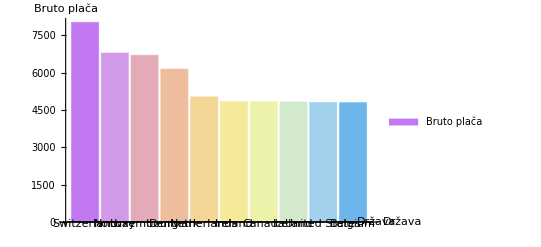

Država | Bruto plača[$]
Switzerland | 8017.7
Norway | 6786.5
Luxembourg | 6694.
Denmark | 6142.4
Netherlands | 5026.2
Ireland | 4838.1
Canada | 4828.3
Iceland | 4824.
United States | 4799.9
Belgium | 4793.

```mathematica
sortiraj2014 = SortBy[data, {-#[[2]]} &];
naj2014 = Take[sortiraj2014, 10];
naj2014Dr = naj2014[[All,1]];
naj2014Pl = naj2014[[All,2]];
drzave2014 = {};
AppendTo[drzave2014,{naj2014Dr,naj2014Pl}];
TableForm[drzave2014, TableHeadings -> {None, {"Država", "Bruto plača[$]"}}]
BarChart[naj2014Pl, ChartLabels -> naj2014Dr, 
  ChartStyle -> "Pastel", 
  ChartLegends -> Placed[{"Bruto plača"}, {0.8, 0.8}],
  AxesLabel -> {"Država", "Bruto plača"}]
```

## 10 držav z navišjo bruto plačo v letu 2015

```mathematica
sortiraj2015 = SortBy[data, {-#[[3]]} &];

naj2015 = Take[sortiraj2015, 10];
naj2015Dr = naj2015[[All,1]];
naj2015Pl = naj2015[[All,3]];
drzave2015 = {};
AppendTo[drzave2015,{naj2015Dr,naj2015Pl}];
TableForm[drzave2015, TableHeadings -> {None, {"Država", "Bruto plača[$]"}}]

BarChart[naj2015Pl, ChartLabels -> naj2015Dr, 
  ChartStyle -> "Pastel", 
  ChartLegends -> Placed[{"Bruto plača"}, {0.8, 0.8}],
  AxesLabel -> {"Država", "Bruto plača"}]
```

Država | Bruto plača[$]
Switzerland
Luxembourg
Norway
Denmark
United States
Iceland
United Kingdom
Netherlands
Canada
Ireland | 7562.3
5675.6
5456.2
5242.3
4932.1
4639.4
4270.5
4257.7
4248.9
4082.6

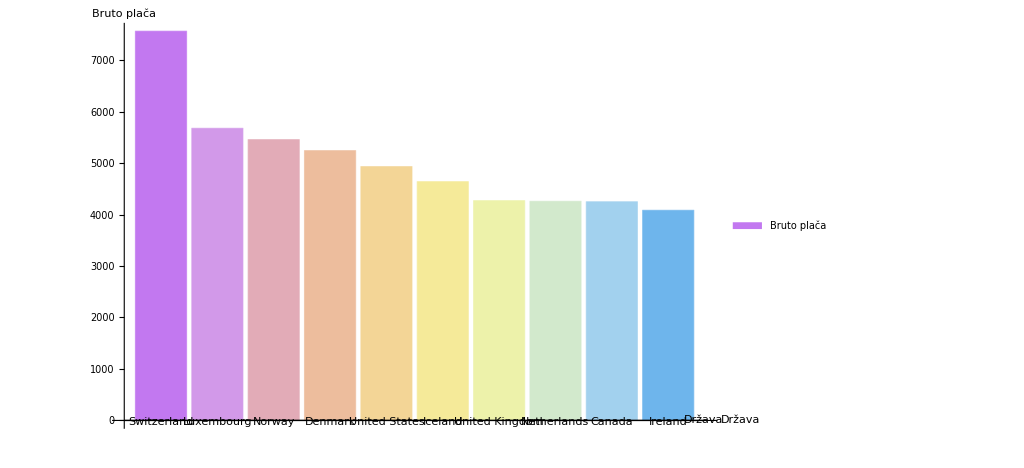

## 10 držav z navišjo bruto plačo v letu 2016

```mathematica
sortiraj2016 = SortBy[data, {-#[[4]]} &];

naj2016 = Take[sortiraj2016, 10];
naj2016Dr = naj2016[[All,1]];
naj2016Pl = naj2016[[All,4]];
drzave2016 = {};
AppendTo[drzave2016,{naj2016Dr,naj2016Pl}];
TableForm[drzave2016, TableHeadings -> {None, {"Država", "Bruto plača[$]"}}]

BarChart[naj2016Pl, ChartLabels -> naj2016Dr, 
  ChartStyle -> "Pastel", 
  ChartLegends -> Placed[{"Bruto plača"}, {0.8, 0.8}],
  AxesLabel -> {"Država", "Bruto plača"}]
```

Država | Bruto plača[$]
Switzerland
Luxembourg
Iceland
Norway
Denmark
United States
Netherlands
Ireland
Belgium
Canada | 7323.2
5690.6
5486.4
5282.7
5251.9
4991.2
4285.5
4147.4
4071.1
4056.5

## 10 držav z navišjo bruto plačo v letu 2017

Država | Bruto plača[$]
Switzerland
Iceland
Luxembourg
Norway
Denmark
United States
Netherlands
Ireland
Canada
Belgium | 7351.3
6619.2
5992.9
5461.7
5440.6
5134.3
4393.3
4320.
4245.4
4197.9

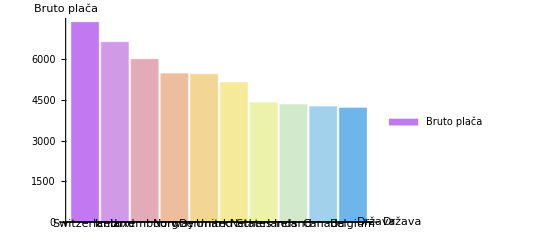

```mathematica
sortiraj2017 = SortBy[data, {-#[[5]]} &];

naj2017 = Take[sortiraj2017, 10];
naj2017Dr = naj2017[[All,1]];
naj2017Pl = naj2017[[All,5]];
drzave2017 = {};
AppendTo[drzave2017,{naj2017Dr,naj2017Pl}];
TableForm[drzave2017, TableHeadings -> {None, {"Država", "Bruto plača[$]"}}]

BarChart[naj2017Pl, ChartLabels -> naj2017Dr, 
  ChartStyle -> "Pastel", 
  ChartLegends -> Placed[{"Bruto plača"}, {0.8, 0.8}],
  AxesLabel -> {"Država", "Bruto plača"}]
```

## 10 držav z navišjo bruto plačo v letu 2018

Država | Bruto plača[$]
Switzerland
Iceland
Luxembourg
Denmark
Norway
United States
Netherlands
Ireland
Belgium
Canada | 7476.4
6704.5
6416.5
5776.
5732.7
5299.1
4654.3
4644.6
4509.3
4400.1

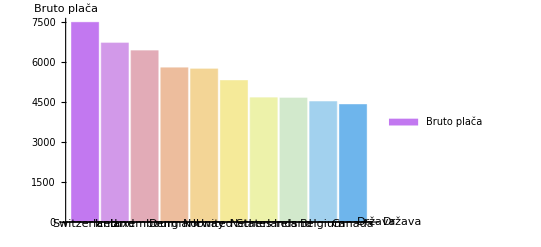

```mathematica
sortiraj2018 = SortBy[data, {-#[[6]]} &];

naj2018 = Take[sortiraj2018, 10];
naj2018Dr = naj2018[[All,1]];
naj2018Pl = naj2018[[All,6]];
drzave2018 = {};
AppendTo[drzave2018,{naj2018Dr,naj2018Pl}];
TableForm[drzave2018, TableHeadings -> {None, {"Država", "Bruto plača[$]"}}]

BarChart[naj2018Pl, ChartLabels -> naj2018Dr, 
  ChartStyle -> "Pastel", 
  ChartLegends -> Placed[{"Bruto plača"}, {0.8, 0.8}],
  AxesLabel -> {"Država", "Bruto plača"}]
```

## 10 držav z navišjo bruto plačo v letu 2019

Država | Bruto plača[$]
Switzerland
Iceland
Luxembourg
Denmark
Norway
United States
Ireland
Netherlands
Canada
Belgium | 7466.2
6149.7
6146.4
5530.
5524.
5466.9
4593.7
4509.7
4395.2
4379.6

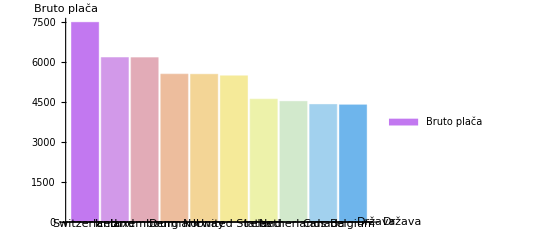

```mathematica
sortiraj2019 = SortBy[data, {-#[[7]]} &];

naj2019 = Take[sortiraj2019, 10];
naj2019Dr = naj2019[[All,1]];
naj2019Pl = naj2019[[All,7]];
drzave2019 = {};
AppendTo[drzave2019,{naj2019Dr,naj2019Pl}];
TableForm[drzave2019, TableHeadings -> {None, {"Država", "Bruto plača[$]"}}]

BarChart[naj2019Pl, ChartLabels -> naj2019Dr, 
  ChartStyle -> "Pastel", 
  ChartLegends -> Placed[{"Bruto plača"}, {0.8, 0.8}],
  AxesLabel -> {"Država", "Bruto plača"}]
```

## 10 držav z navišjo bruto plačo v letu 2020

Država | Bruto plača[$]
Switzerland
Luxembourg
Iceland
United States
Denmark
Norway
Netherlands
Ireland
Canada
Belgium | 7712.7
6228.8
5862.5
5782.6
5701.1
5247.5
4764.8
4681.6
4489.7
4352.7

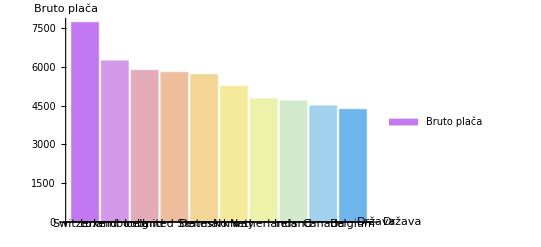

ListLinePlot::invdrange: {2014,2015,2016,2017,2018,2019,2020} must be of the form {xmin, xmax}.

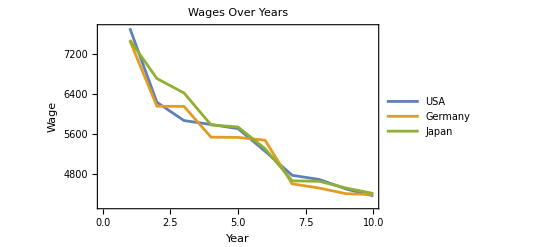

```mathematica
sortiraj2020 = SortBy[data, {-#[[8]]} &];

naj2020 = Take[sortiraj2020, 10];
naj2020Dr = naj2020[[All,1]];
naj2020Pl = naj2020[[All,8]];
drzave2020 = {};
AppendTo[drzave2020,{naj2020Dr,naj2020Pl}];
TableForm[drzave2020, TableHeadings -> {None, {"Država", "Bruto plača[$]"}}]

BarChart[naj2020Pl, ChartLabels -> naj2020Dr, 
  ChartStyle -> "Pastel", 
  ChartLegends -> Placed[{"Bruto plača"}, {0.8, 0.8}],
  AxesLabel -> {"Država", "Bruto plača"}]
  
 ListLinePlot[{naj2020Pl, naj2019Pl, naj2018Pl,naj2017Pl,naj2016Pl,naj2015Pl,naj2014Pl}, 
  DataRange -> letaSvet, 
  PlotLegends -> {"USA", "Germany", "Japan"}, 
  Frame -> True, 
  FrameLabel -> {"Year", "Wage"}, 
  PlotLabel -> "Wages Over Years"]
```

## Povprečna plača za vsako leto

```mathematica
placaPovp = Mean[Drop[data[[All,2]],1]];

DynamicModule[{year, result},
  Column[{
    Row[{"Vpišite leto: ", InputField[Dynamic[year], Number]}],
    Button["Išči", result = Mean[Drop[data[[All,year-2012]],1]]],
    Row[{"Povprečna plača: ", Dynamic[result]}]
  }]
]
```